```mathematica
Integrate[Sin[x]/x,{x,0,10}]
```

```mathematica
SinIntegral[10] // N
```

1.65835

```mathematica
Integrate[x y^2 Log[1+x^2+y^2],{x,0,Sqrt[3-y^2]},{y,0,Sqrt[3]}] // N
```

ConditionalExpression[0.166667 (1.73205 (-16.6355-3. y^2+y^4-3. (-7.+y^2) Log[7.-1. y^2])+0.0666667 (12.5664-12. (4.-1. y^2)^(5/2) ArcTan[1.73205/(√(4.-1. y^2))]-5.19615 (-27.9533-2. y^2+y^4+18. Log[7.-1. y^2]))), ]

```mathematica
x = r Cos[t];
y = r Sin[t];
```

```mathematica
Clear[r,t]
```

```mathematica
Integrate[r *(x y^2 Log[1+x^2+y^2]),{r,0,Sqrt[3]},{t,0,Pi/2}]  //N
```

1.16461

```mathematica
ClearAll"Global`*"
```

```mathematica
"Global`*"  ClearAll
Clear[x,y,z,t,r,s,u,v]
```

Global`*  ClearAll

```mathematica
ch[x_,y_] := Boole[-10< 6 x +7 y &&6 x +7 y  < 10 && -6< 3 x +6 y &&3 x +6 y<6]
Plot3D[ch[x,y], {x, -10, 10}, {y, -10,10}]
```

-Graphics3D-

```mathematica
f[x_,y_] := (18 x^2+57 x y+42 y^2)^4
```

```mathematica
Integrate[f[x,y] ch[x,y], {x, -100,100},{y,-100,100}] // N
```

8.2944×10^6

```mathematica
punkter = RandomReal[{-1,1},{100000,2}];
First[punkter]
test[{x_,y_}] := x^4 +y^4 + 62 x^2 y^2 <=1;
```

{0.595959,-0.78793}

```mathematica
test[{1,1}]
test[{0,0}]
```

False

True

```mathematica
iOmrade = Select [punkter, test];
ejIOmrade = Complement[punkter, iOmrade];
```

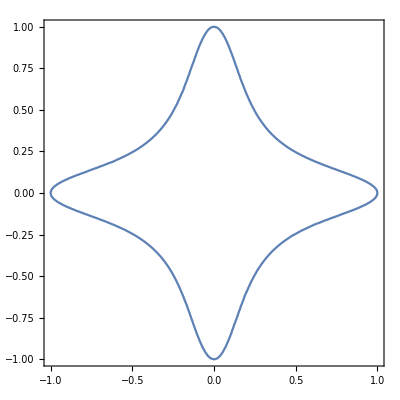

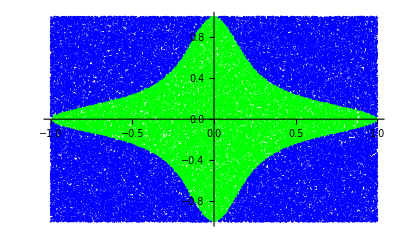

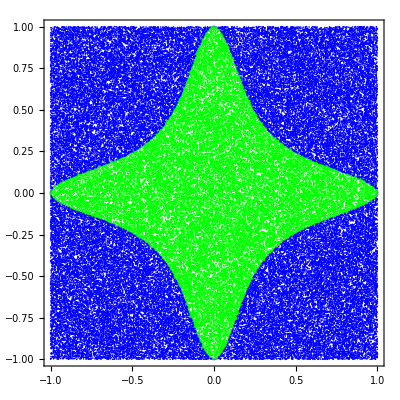

```mathematica
p1 = ContourPlot[x^4 +y^4 + 62 x^2 y^2 ==1, {x,-1,1},{y,-1,1}]
p2 = ListPlot[{iOmrade, ejIOmrade}, PlotStyle -> {Green, Blue}]
Show[p1,p2]
```

```mathematica
antal = Length[iOmrade]
```

34895

```mathematica
area = N[(antal*4)/100000]
```

1.3958

```mathematica
g[r_] := 2 r^2 Pi
```

```mathematica
Integrate[g[r],{r,-1,1}]
```

(4 π)/3

```mathematica
Integrate[g[r],r]
```

(2 π r^3)/3

```mathematica
ch2[x_,y_] := Boole[x^2 + y^2 < 1]
```

SetDelayed::write: Tag Boole in Boole[x^2+y^2<1][x_,y_] is Protected.

$Failed

```mathematica
Plot3D[ch2[x,y], {x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
h[r_] := 4 Pi r^2
```

```mathematica
h[r]
```

4 π r^2

```mathematica
Integrate[h[r],{r,0,1}]
```

(4 π)/3

```mathematica
Integrate [ {4 Pi r^3 /3}, {r,0,1}]
```

{π/3}

```mathematica
Integrate[{Pi r^4 / 3},{r,0,1}]
```

{π/15}

```mathematica
Clear[x,y,z,h,t,s,a,b]
```

```mathematica
Clear[r]
funktion := Boole[0< x && x<y]
```

```mathematica
Integrate[t^z Log[t] funktion, {t,x,y}, Assumptions->z== Integers]
```

(Boole[x>0&&x<y] (x^(1+z) (1-(1+z) Log[x])+y^(1+z) (-1+(1+z) Log[y])))/(1+z)^2

```mathematica
Integrate[t^z Log[t] , {t,x,y}, Assumptions->z== Integers]
```

(x^(1+z) (1-(1+z) Log[x])+y^(1+z) (-1+(1+z) Log[y]))/(1+z)^2

```mathematica
funktion2 := Boole[x1^2 + x2^2 + x3^2≤ 1]
```

```mathematica
Integrate[funktion2,, {x1,-1,1},{x2,-1,1},{x3,-1,1}]
```

(4 Null π)/3

```mathematica
funktion3:= Boole[x1^2 + x2^2 + x3^2 + x4^2≤ 1]
```

```mathematica
Integrate[funktion3,, {x1,-1,1},{x2,-1,1},{x3,-1,1},{x4,-1,1}]
```

(Null π^2)/2

```mathematica
funktion4 := Boole[x1^2 + x2^2 + x3^2 + x4^2+x5^2≤ 1]
Integrate[funktion4,, {x1,-1,1},{x2,-1,1},{x3,-1,1},{x4,-1,1},{x5,-1,1}]
```

(8 Null π^2)/15

```mathematica
nyaPunkter = RandomReal[{-1,1},{100000,10}];
test2[{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_}] := x1^2 +x2^2 +  x3^2+ x4^2 + x5^2+ x6^2+ x7^2+ x8^2+ x9^2+ x10^2<=1;
iNyaOmrade = Select [nyaPunkter, test2];
ejINyaOmrade = Complement[nyaPunkter, iNyaOmrade];
```

```mathematica
antal2=Length[iNyaOmrade]
```

242

```mathematica
area2 = antal2/100000 2^10
```

7744/3125

```mathematica
minIntegrand [x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_] := x1^2 +x2^2 +  x3^2+ x4^2 + x5^2+ x6^2+ x7^2+ x8^2+ x9^2+ x10^2
```

```mathematica
NIntegrate[Boole[minIntegrand[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10]], {x1,-1,1},{x2,-1,1},{x3,-1,1},{x4,-1,1},{x5,-1,1},{x6,-1,1},{x7,-1,1},{x8,-1,1},{x9,-1,1},{x10,-1,1}, Method-> QuasiMonteCarlo]
```

NIntegrate::inumr: The integrand Boole[minIntegrand[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

```mathematica
NIntegrate[Boole[minIntegrand[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10]≤ 1],{x1,-1,1},{x2,-1,1},{x3,-1,1},{x4,-1,1},{x5,-1,1},{x6,-1,1},{x7,-1,1},{x8,-1,1},{x9,-1,1},{x10,-1,1},Method->QuasiMonteCarlo]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 2.70397 and 0.252916 for the integral and error estimates.

2.70397

```mathematica
Pi^5/120 // N
```

2.55016